#### Latham's a(eta) solution

6.08623

7.6189

0.+0. ⅈ

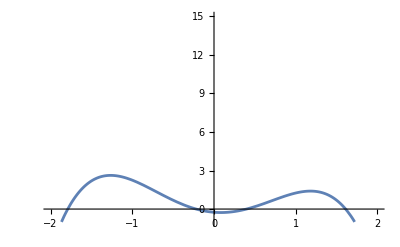

{{a→-1.78923},{a→-0.218388},{a→0.397315},{a→1.61031}}

{1.61031+0. ⅈ,0.397315+0. ⅈ,-0.218388+0. ⅈ,-1.78923+0. ⅈ}

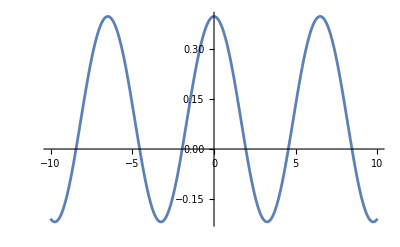

```mathematica
(* Closed, kappa > 0, 4 real roots: 2 kt^3/mt^2 > gp(x) > gm(x) *)
(* In this case, there is a contour satisfying Witten's criterion. *)

(* For turning universe (cc=0) *)
Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1.;
m=.5;
x=1;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-1,15}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau,mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau,mm]^2)
Plot[Re[a[tau]],{tau,-10,10}]
```

-0.5

2.×10^-12

0.+0. ⅈ

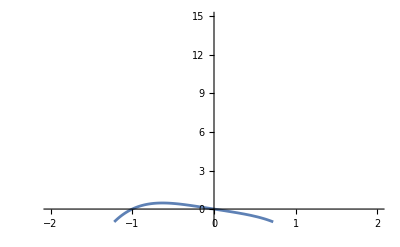

{{a→-1.00007},{a→-0.0001},{a→0.500083-0.865939 ⅈ},{a→0.500083+0.865939 ⅈ}}

{0.500083+0.865939 ⅈ,0.500083-0.865939 ⅈ,-0.0001,-1.00007}

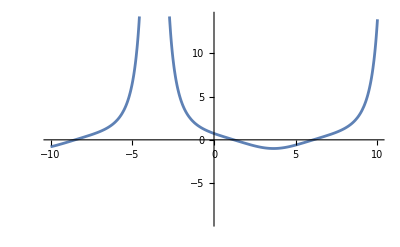

```mathematica
(* Closed, kappa > 0, 4 real roots: 2 kt^3/mt^2 > gp(x) > gm(x) *)
(* In this case, there is a contour satisfying Witten's criterion. *)

(* For universe with de-Sitter boundary (cc=i/2 K(1-m)) *)
Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm,cc]

lam=1.;
k=0.0001;
m=1.;
r=0.0001;
x=k r/m^3;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-1,15}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
cc = I/2 EllipticK[1-mm];
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+cc,mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+cc,mm]^2)
Plot[Re[1/a[tau]],{tau,-10,10}]
```

#### Lasenby’s a(eta) solution

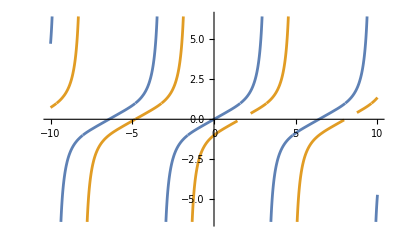

```mathematica
(* Radiation, assume Lambda=r=1 *)
Clear[s] (* s=1/a, tau_FCB=0 *)
s[tau_]:=JacobiSN[ tau/Sqrt[3],1/2]/JacobiCN[tau/Sqrt[3],1/2] JacobiDN[ tau/Sqrt[3],1/2]
Plot[{Re[s[tau]],-1/a[tau]},{tau,-10,10}]
```

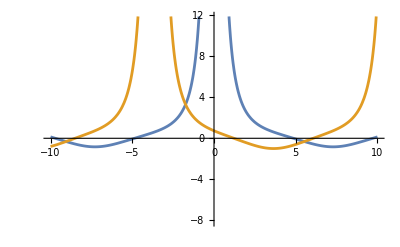

```mathematica
(* CDM, assume Lambda=m=1 *)
Clear[s] (* s=1/a *)
s[tau_]:=WeierstrassP[tau,{0,-1/432}]
Plot[{Re[10*s[tau]],Re[1/a[tau]]},{tau,-10,10}]
```